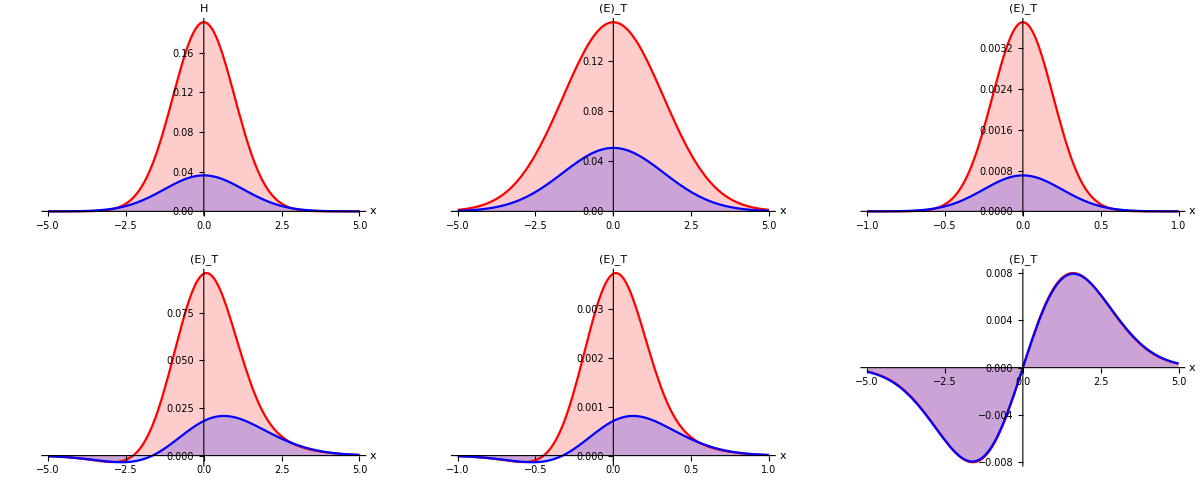

```mathematica
x=0.4; t=0.1; xmin=-5; xmax=5;

plotHDeN=Plot[{HDeNu[x,bx,0.],    HDeNd[x,bx,0.]},{bx,xmin,xmax},Filling->Axis,PlotRange->All,PlotStyle->{Red,Blue},AxesLabel->{"x","H"}];
plotETDeN=Plot[{ETDeNu[x,bx,0.],    ETDeNd[x,bx,0.]},{bx,xmin,xmax},Filling->Axis,PlotRange->All,PlotStyle->{Red,Blue},AxesLabel->{"x","(Ē)_T"}];
plotDenXYpx=Plot[{DenXYu[x,bx,0.],DenXYd[x,bx,0.]},{bx,-1.,1.},Filling->Axis,PlotRange->{0,All},PlotStyle->{Red,Blue},AxesLabel->{"x","(Ē)_T"}];
plotDeN=Plot[{DeNu[x,0.,by],DeNd[x,0.,by]},{by,xmin,xmax},Filling->Axis,PlotRange->All,PlotStyle->{Red,Blue},AxesLabel->{"x","(Ē)_T"}];
plotDENXYpy=Plot[{DenXYu[x,0.,by],DenXYd[x,0.,by]},{by,-1.,1.},Filling->Axis,PlotRange->All,PlotStyle->{Red,Blue},AxesLabel->{"x","(Ē)_T"}];
plotDENETpy=Plot[{DeNETu[x,0.,by],DeNETd[x,0.,by]},{by,xmin,xmax},Filling->Axis,PlotRange->All,PlotStyle->{Red,Blue},AxesLabel->{"x","(Ē)_T"}];

GraphicsGrid[{{plotHDeN,plotETDeN,plotDenXYpx},{plotDeN,plotDENXYpy,plotDENETpy}},ImageSize->Full,PlotLabel->Style[StandardForm[xz],FontSize->25,FontColor->Black]]
```